```mathematica
rootfolder=NotebookDirectory[];
```

## import color palette

```mathematica
palette=ImageData[Import[StringJoin[rootfolder,"neon.png"]]];
palette=Extract[palette,1];
smoothpalette=Interpolation[Table[{(i-1)/(Length[palette]-1),{Extract[Extract[palette,i],1],Extract[Extract[palette,i],2],Extract[Extract[palette,i],3]}},{i,1,Length[palette]}],InterpolationOrder->1];
neon[x_]:=RGBColor[smoothpalette[x]];
```

## north

```mathematica
northhistory=Import[StringJoin[rootfolder,"NH_seaice_extent_final_v2.csv"],"CSV"];
```

```mathematica
northnow=Import[StringJoin[rootfolder,"NH_seaice_extent_nrt_v2.csv"],"CSV"];
northnow2=northnow[[3;;Length[northnow],{1,2,3,4}]];
```

```mathematica
northhistory2=northhistory[[3;;Length[northhistory],{1,2,3,4}]];
monthdays={31,28,31,30,31,30,31,31,30,31,30,31};
```

```mathematica
years=Union[northhistory2[[All,1]]];
y=0;Label[yloop];y=y+1;temp=Select[northhistory2,#[[1]]==years[[y]]&];Subscript[ndata, y]=Table[{Sum[Extract[monthdays,j],{j,1,Extract[Extract[temp,i],2]-1}]+Extract[Extract[temp,i],3]-0.5,Extract[Extract[temp,i],4]},{i,1,Length[temp]}];If[y<Length[years],Goto[yloop]];
```

```mathematica
temp=northnow2;Subscript[ndata, Length[years]+1]=Table[{Sum[Extract[monthdays,j],{j,1,Extract[Extract[temp,i],2]-1}]+Extract[Extract[temp,i],3]-0.5,Extract[Extract[temp,i],4]},{i,1,Length[temp]}];
```

```mathematica
means=Table[Mean[Select[Subscript[ndata, j],#[[1]]≤First[Last[Subscript[ndata, Length[years]+1]]]&]][[2]],{j,1,Length[years]+1}];
minmean=Min[means[[2;;Length[means]]]];
maxmean=Max[means[[2;;Length[means]]]];
```

```mathematica
ymin=Min[Table[Min[Subscript[ndata, jj][[All,2]]],{jj,1,Length[years]+1}]]-0.5;
ymax=Max[Table[Max[Subscript[ndata, jj][[All,2]]],{jj,1,Length[years]+1}]]+0.5;
```

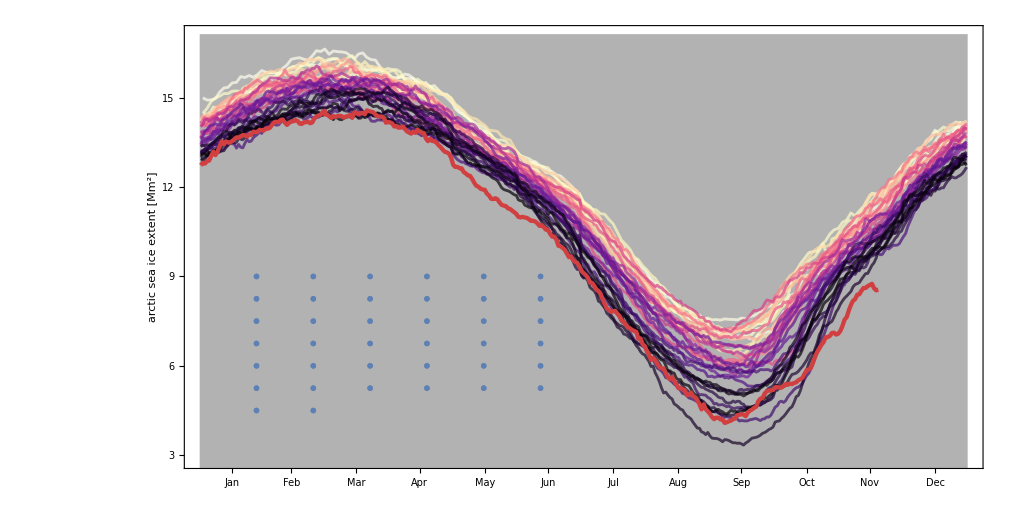

```mathematica
xticks={{15.5,"Jan"},{43.5,"Feb"},{74.5,"Mar"},{104.5,"Apr"},{135.5,"May"},{165.5,"Jun"},{196.5,"Jul"},{227.5,"Aug"},{257.5,"Sep"},{288.5,"Oct"},{318.5,"Nov"},{349.5,"Dec"}};
xticks2=Table[{Extract[Extract[xticks,i],1],""},{i,1,Length[xticks]}];
ystep=3;
yticks=Table[{i,ToString[i]},{i,0,Ceiling[ymax,ystep],ystep}];
yticks2=Table[{Extract[Extract[yticks,i],1],""},{i,1,Length[yticks]}];
plotrange={{0,365},{ymin,ymax}};
op=0.7;xlegstep=27;xlegstart=0;ylegstep=0.75;ylegstart=9;legcols=6;legrows=Ceiling[Length[years]/legcols];
northplot=Show[Plot[ymax+1,{x,0,365},Filling->0,FillingStyle->Directive[Gray,Opacity[0.6]],PlotRange->plotrange,Frame->True,ImageSize->{1024,512},AspectRatio->0.5,BaseStyle->{FontFamily->"Helvetica Neue",FontSize->24,FontWeight->"Thin"},FrameTicks->{{yticks,yticks2},{xticks,xticks2}},FrameLabel->{None,"arctic sea ice extent [Mm^2]"}],Table[ListPlot[Subscript[ndata, j],Joined->True,PlotStyle->Directive[neon[(j-1)/Length[years]],Opacity[op],Thickness[0.002]]],{j,2,Length[years]}],ListPlot[Subscript[ndata, Length[years]+1],Joined->True,PlotStyle->Directive[ColorData["CherryTones"][0.4],Opacity[1],Thickness[0.003]]],Flatten[Table[Table[ListPlot[{{xlegstart+(j-1)xlegstep-legcols(z-1)xlegstep,ylegstart-(z-1)ylegstep}},PlotMarkers->Style[ToString[years[[j]]],neon[(j-1)/Length[years]],Italic,FontFamily->"Helvetica Neue",FontSize->24,FontWeight->"Thin"]],{j,2+legcols(z-1),Min[Length[years],1+legcols z]}],{z,1,legrows}],1],ListPlot[{{xlegstart+((Length[years]+1)-1)xlegstep-legcols(legrows-1)xlegstep,ylegstart-(legrows-1)ylegstep}},PlotMarkers->Style[ToString["2016"],ColorData["CherryTones"][0.4],Italic,FontFamily->"Helvetica Neue",FontSize->24,FontWeight->"Thin"]]]
```

## south

```mathematica
southhistory=Import[StringJoin[rootfolder,"SH_seaice_extent_final_v2.csv"],"CSV"];
```

```mathematica
southnow=Import[StringJoin[rootfolder,"SH_seaice_extent_nrt_v2.csv"],"CSV"];
southnow2=southnow[[3;;Length[southnow],{1,2,3,4}]];
```

```mathematica
southhistory2=southhistory[[3;;Length[southhistory],{1,2,3,4}]];
monthdays={31,28,31,30,31,30,31,31,30,31,30,31};
```

```mathematica
years=Union[southhistory2[[All,1]]];
y=0;Label[yloop];y=y+1;temp=Select[southhistory2,#[[1]]==years[[y]]&];Subscript[sdata, y]=Table[{Sum[Extract[monthdays,j],{j,1,Extract[Extract[temp,i],2]-1}]+Extract[Extract[temp,i],3]-0.5,Extract[Extract[temp,i],4]},{i,1,Length[temp]}];If[y<Length[years],Goto[yloop]];
```

```mathematica
temp=southnow2;Subscript[sdata, Length[years]+1]=Table[{Sum[Extract[monthdays,j],{j,1,Extract[Extract[temp,i],2]-1}]+Extract[Extract[temp,i],3]-0.5,Extract[Extract[temp,i],4]},{i,1,Length[temp]}];
```

```mathematica
means=Table[Mean[Select[Subscript[sdata, j],#[[1]]≤First[Last[Subscript[sdata, Length[years]+1]]]&]][[2]],{j,1,Length[years]+1}];
minmean=Min[means[[2;;Length[means]]]];
maxmean=Max[means[[2;;Length[means]]]];
```

```mathematica
ymin=Min[Table[Min[Subscript[sdata, jj][[All,2]]],{jj,1,Length[years]+1}]]-0.5;
ymax=Max[Table[Max[Subscript[sdata, jj][[All,2]]],{jj,1,Length[years]+1}]]+0.5;
```

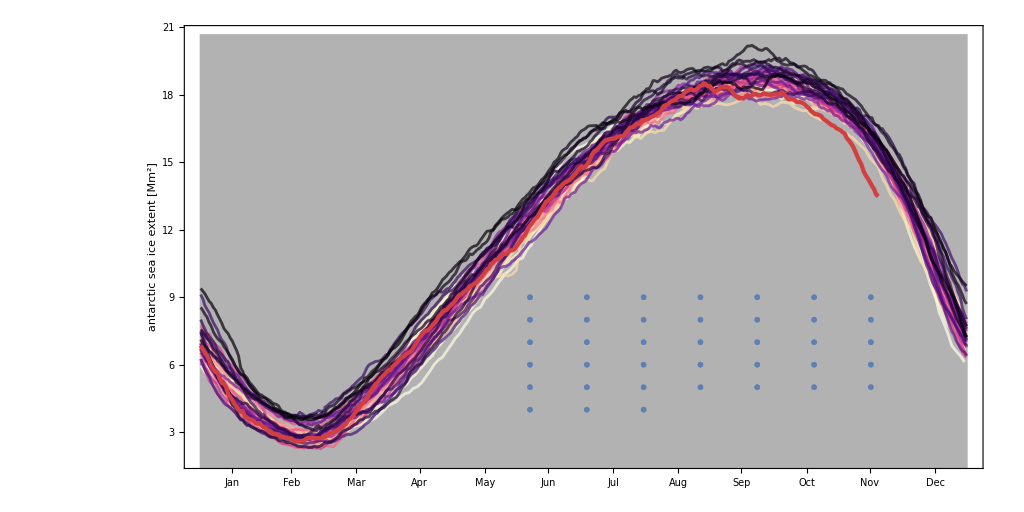

```mathematica
xticks={{15.5,"Jan"},{43.5,"Feb"},{74.5,"Mar"},{104.5,"Apr"},{135.5,"May"},{165.5,"Jun"},{196.5,"Jul"},{227.5,"Aug"},{257.5,"Sep"},{288.5,"Oct"},{318.5,"Nov"},{349.5,"Dec"}};
xticks2=Table[{Extract[Extract[xticks,i],1],""},{i,1,Length[xticks]}];
ystep=3;
yticks=Table[{i,ToString[i]},{i,0,Ceiling[ymax,ystep],ystep}];
yticks2=Table[{Extract[Extract[yticks,i],1],""},{i,1,Length[yticks]}];
plotrange={{0,365},{ymin,ymax}};
op=0.7;xlegstep=27;xlegstart=130;ylegstep=1;ylegstart=9;legcols=7;legrows=Ceiling[Length[years]/legcols];
southplot=Show[Plot[ymax+1,{x,0,365},Filling->0,FillingStyle->Directive[Gray,Opacity[0.6]],PlotRange->plotrange,Frame->True,ImageSize->{1024,512},AspectRatio->0.5,BaseStyle->{FontFamily->"Helvetica Neue",FontSize->24,FontWeight->"Thin"},FrameTicks->{{yticks,yticks2},{xticks,xticks2}},FrameLabel->{None,"antarctic sea ice extent [Mm^2]"}],Table[ListPlot[Subscript[sdata, j],Joined->True,PlotStyle->Directive[neon[(j-1)/Length[years]],Opacity[op],Thickness[0.002]]],{j,2,Length[years]}],ListPlot[Subscript[sdata, Length[years]+1],Joined->True,PlotStyle->Directive[ColorData["CherryTones"][0.4],Opacity[1],Thickness[0.003]]],Flatten[Table[Table[ListPlot[{{xlegstart+(j-1)xlegstep-legcols(z-1)xlegstep,ylegstart-(z-1)ylegstep}},PlotMarkers->Style[ToString[years[[j]]],neon[(j-1)/Length[years]],Italic,FontFamily->"Helvetica Neue",FontSize->24,FontWeight->"Thin"]],{j,2+legcols(z-1),Min[Length[years],1+legcols z]}],{z,1,legrows}],1],ListPlot[{{xlegstart+((Length[years]+1)-1)xlegstep-legcols(legrows-1)xlegstep,ylegstart-(legrows-1)ylegstep}},PlotMarkers->Style[ToString["2016"],ColorData["CherryTones"][0.4],Italic,FontFamily->"Helvetica Neue",FontSize->24,FontWeight->"Thin"]]]
```

## global

```mathematica
y=0;Label[yloop];y=y+1;Subscript[gdata, y]=Table[{Extract[Extract[Subscript[ndata, y],i],1],Extract[Extract[Subscript[ndata, y],i],2]+Extract[Extract[Subscript[sdata, y],i],2]},{i,1,Length[Subscript[ndata, y]]}];If[y<Length[years]+1,Goto[yloop]];
```

```mathematica
means=Table[Mean[Select[Subscript[gdata, j],#[[1]]≤First[Last[Subscript[gdata, Length[years]+1]]]&]][[2]],{j,1,Length[years]+1}];
minmean=Min[means[[2;;Length[means]]]];
maxmean=Max[means[[2;;Length[means]]]];
```

```mathematica
ymin=Min[Table[Min[Subscript[gdata, jj][[All,2]]],{jj,1,Length[years]+1}]]-0.5;
ymax=Max[Table[Max[Subscript[gdata, jj][[All,2]]],{jj,1,Length[years]+1}]]+0.5;
```

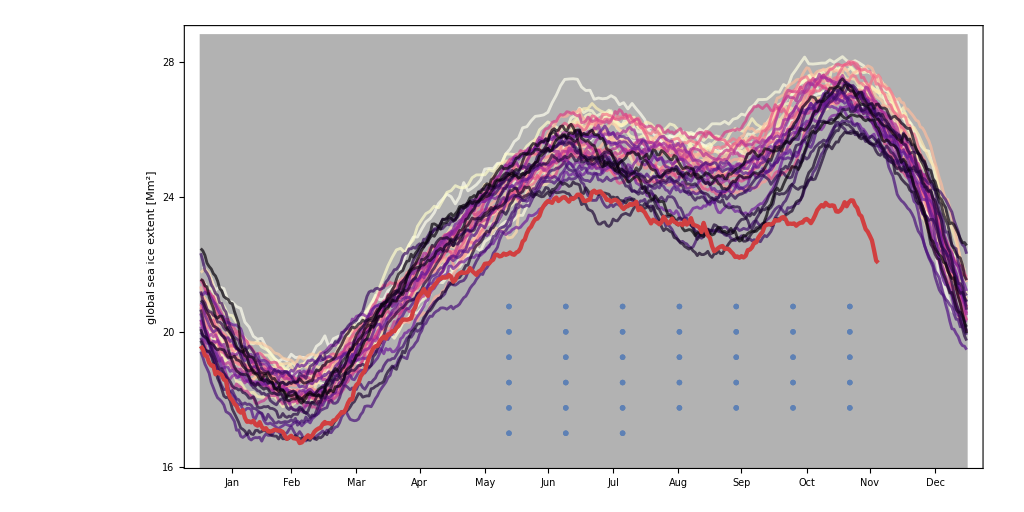

```mathematica
xticks={{15.5,"Jan"},{43.5,"Feb"},{74.5,"Mar"},{104.5,"Apr"},{135.5,"May"},{165.5,"Jun"},{196.5,"Jul"},{227.5,"Aug"},{257.5,"Sep"},{288.5,"Oct"},{318.5,"Nov"},{349.5,"Dec"}};
xticks2=Table[{Extract[Extract[xticks,i],1],""},{i,1,Length[xticks]}];
ystep=2;
yticks=Table[{i,ToString[i]},{i,0,Ceiling[ymax,ystep],ystep}];
yticks2=Table[{Extract[Extract[yticks,i],1],""},{i,1,Length[yticks]}];
plotrange={{0,365},{ymin,ymax}};
op=0.7;xlegstep=27;xlegstart=120;ylegstep=0.75;ylegstart=20.75;legcols=7;legrows=Ceiling[Length[years]/legcols];
globalplot=Show[Plot[ymax+1,{x,0,365},Filling->0,FillingStyle->Directive[Gray,Opacity[0.6]],PlotRange->plotrange,Frame->True,ImageSize->{1024,512},AspectRatio->0.5,BaseStyle->{FontFamily->"Helvetica Neue",FontSize->24,FontWeight->"Thin"},FrameTicks->{{yticks,yticks2},{xticks,xticks2}},FrameLabel->{None,"global sea ice extent [Mm^2]"}],Table[ListPlot[Subscript[gdata, j],Joined->True,PlotStyle->Directive[neon[(j-1)/Length[years]],Opacity[op],Thickness[0.002]]],{j,2,Length[years]}],ListPlot[Subscript[gdata, Length[years]+1],Joined->True,PlotStyle->Directive[ColorData["CherryTones"][0.4],Opacity[1],Thickness[0.003]]],Flatten[Table[Table[ListPlot[{{xlegstart+(j-1)xlegstep-legcols(z-1)xlegstep,ylegstart-(z-1)ylegstep}},PlotMarkers->Style[ToString[years[[j]]],neon[(j-1)/Length[years]],Italic,FontFamily->"Helvetica Neue",FontSize->24,FontWeight->"Thin"]],{j,2+legcols(z-1),Min[Length[years],1+legcols z]}],{z,1,legrows}],1],ListPlot[{{xlegstart+((Length[years]+1)-1)xlegstep-legcols(legrows-1)xlegstep,ylegstart-(legrows-1)ylegstep}},PlotMarkers->Style[ToString["2016"],ColorData["CherryTones"][0.4],Italic,FontFamily->"Helvetica Neue",FontSize->24,FontWeight->"Thin"]]]
```